```mathematica
xbar[ka_,x_]:=(ka*x)/(1+(ka*x))
```

```mathematica
xrange=Table[Power[10,-ii],{ii,0,15,0.01}];
```

```mathematica
ka10pow3=ListLinePlot[Table[{Log[x],xbar[10^3,x]},{x,xrange}]];
ka10pow6=ListLinePlot[Table[{Log[x],xbar[10^6,x]},{x,xrange}],PlotStyle->Red];
ka10pow9=ListLinePlot[Table[{Log[x],xbar[10^9,x]},{x,xrange}],PlotStyle->Green];
ka10pow12=ListLinePlot[Table[{Log[x],xbar[10^12,x]},{x,xrange}],PlotStyle->Purple];
```

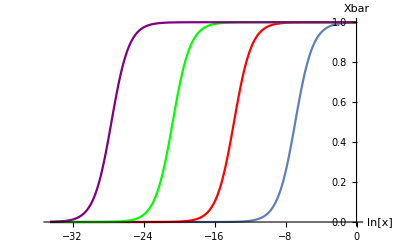

```mathematica
Show[ka10pow3,ka10pow6,ka10pow9,ka10pow12,AxesLabel->{"ln[x]","Xbar"}]
```

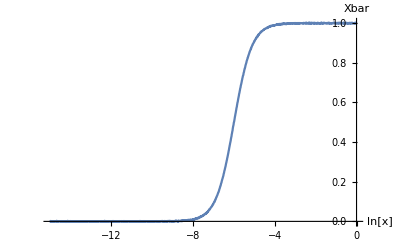

| Estimate | Standard Error | t-Statistic | P-Value
ka | 1.00045×10^6 | 388.073 | 2578. | 2.42166977986×10^-2737

```mathematica
(*0.1% error*)
error=RandomVariate[NormalDistribution[0,0.001],Length[xrange]];
datawitherror=error+Table[xbar[10^6,x],{x,xrange}];
data=Transpose[{Log10[xrange],datawitherror}];
ListLinePlot[data,AxesLabel->{"ln[x]","Xbar"}]
nlm1=NonlinearModelFit[Transpose[{xrange,datawitherror}],(ka*x)/(1+(ka*x)),ka,x];
nlm1["ParameterTable"]
```

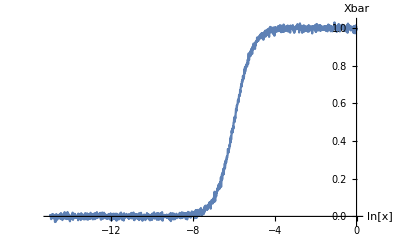

| Estimate | Standard Error | t-Statistic | P-Value
ka | 994410. | 3725.83 | 266.896 | 1.21695011301×10^-1266

```mathematica
(*1% error*)
error=RandomVariate[NormalDistribution[0,0.01],Length[xrange]];
datawitherror=error+Table[xbar[10^6,x],{x,xrange}];
data=Transpose[{Log10[xrange],datawitherror}];
ListLinePlot[data,AxesLabel->{"ln[x]","Xbar"}]
nlm2=NonlinearModelFit[Transpose[{xrange,datawitherror}],(ka*x)/(1+(ka*x)),ka,x];
nlm2["ParameterTable"]
```

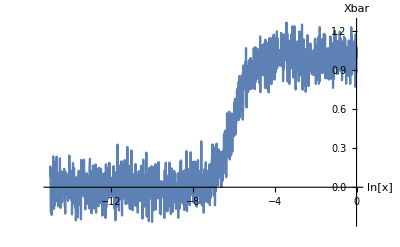

| Estimate | Standard Error | t-Statistic | P-Value
ka | 1.03837×10^6 | 39326.3 | 26.4039 | 1.71198×10^-126

```mathematica
(*10% error*)
error=RandomVariate[NormalDistribution[0,0.1],Length[xrange]];
datawitherror=error+Table[xbar[10^6,x],{x,xrange}];
data=Transpose[{Log10[xrange],datawitherror}];
ListLinePlot[data,AxesLabel->{"ln[x]","Xbar"}]
nlm3=NonlinearModelFit[Transpose[{xrange,datawitherror}],(ka*x)/(1+(ka*x)),ka,x];
nlm3["ParameterTable"]
```